#### (Quit the Kernel then run the cells) Phase-Plots illustration of the dynamics of different regions in the Bif Map (EcoEvo)

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
Format[w] :=ω;
Format[xi]:=ξ;

<<EcoEvo`
(*EcoEvoDocs;*)
ClearParameters;UnsetModel; 
SetModel[{Pop[s]->{Equation:>(-(i s β)/(1+i xi)+Λ-s μ),Color->Green},Pop[i]->{Equation:>(-(i α)/(i+w)+(i s β)/(1+i xi)-i (γ+δ+μ)),Color->Blue},
 Parameters:>(cp={Λ>0,δ>0,γ>0,β>0,xi>0,w>0,μ>0,α>0})}]
equi=SolveEcoEq[];
```

EcoEvo Package Version 1.6.4 (November 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

#### Phase plot of the region II:

Fixed points:

{{s→133.333,i→0.},{s→85.4965,i→6.75961}}

Eigenvalues of FP:

{{-0.12,0.0501961},{0.00887972+0.13495 ⅈ,0.00887972-0.13495 ⅈ}}

Time plot around E2

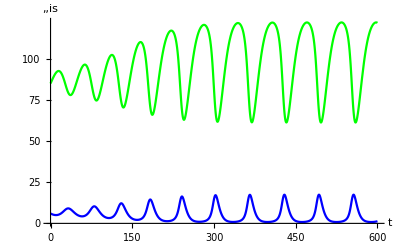

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

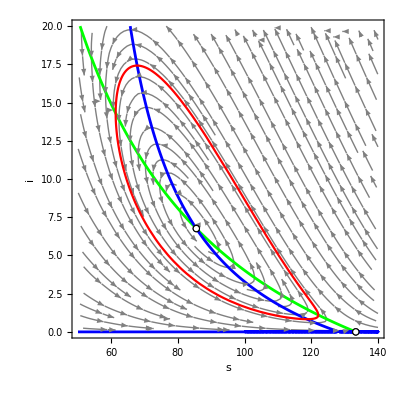

Final time slice is

63.5035

The floquet exponents are

{-3.20788×10^-8,-0.0228667}

spR2E.pdf

solT2.pdf

```mathematica
ClearParameters;
T=600;
xM=140;
xm=50;
yM=20;
ym=0;
Λ=16 ;δ=1/5;γ=3/25;β=1/100;xi=1/1000;μ=3/25;w=51/8 ;α=43/8;
Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
EcoEigenvalues[eq]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[lc,{s,i},PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spR2E.pdf",sp]

Export["solT2.pdf",psol]
```

#### Phase plot of the region III:

Fixed points:

{{s→133.333,i→0.},{s→45.58,i→23.6495}}

Eigenvalues of FP:

{{0.867292,-0.12},{-0.178557+0.265984 ⅈ,-0.178557-0.265984 ⅈ}}

Time plot around E2

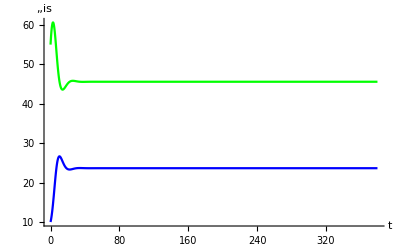

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

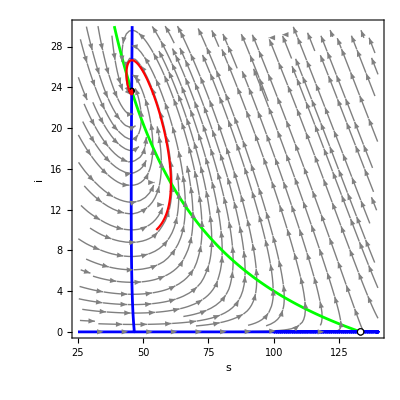

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spR3E.pdf

solT3.pdf

```mathematica
ClearParameters;
T=380;
xM=140;
xm=25;
yM=30;
ym=0;
Λ=16 ;δ=1/5;γ=3/25;β=1/100;xi=1/1000;μ=3/25;
w=6 ;α=5/32;
Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
EcoEigenvalues[eq]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->55,i->10},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spR3E.pdf",sp]

Export["solT3.pdf",psol]
```

#### Phase plot of the boundary TrE2=0 between Regions II and III:

Fixed points:

{{s→133.333,i→0.},{s→80.6403,i→7.90317}}

Eigenvalues of FP:

{{-0.12,0.0589583},{-2.18656×10^-7+0.15125 ⅈ,-2.18656×10^-7-0.15125 ⅈ}}

Time plot around E2

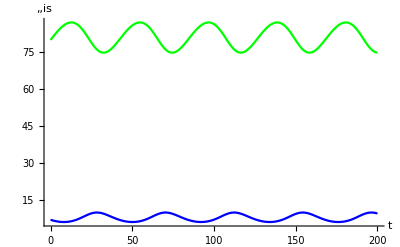

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

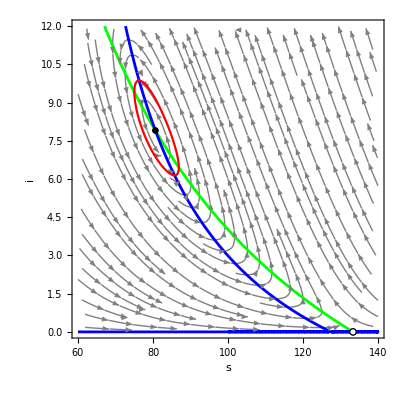

Final time slice is

41.9535

The floquet exponents are

{-0.0000160967+0.0000921828 ⅈ,-0.0000160967-0.0000921828 ⅈ}

spB23E.pdf

solT23.pdf

```mathematica
ClearParameters;
T=200;
xM=140;
xm=60;
yM=12;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=6 ;α=Rationalize[5.00625];

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[lc,{s,i},PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB23E.pdf",sp]
Export["solT23.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions I and II ( between 0 and B1):

4.62051

4.12766

Fixed points:

{{s→133.333,i→0.},{s→72.8175,i→10.0732},{s→133.333,i→0.}}

Eigenvalues of FP:

{{-0.12,0},{-0.017169+0.173632 ⅈ,-0.017169-0.173632 ⅈ},{-0.12,0}}

Time plot around E2

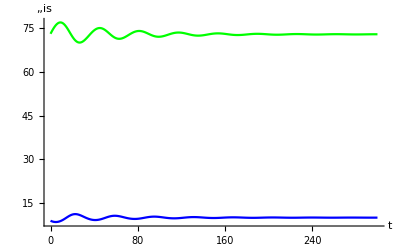

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

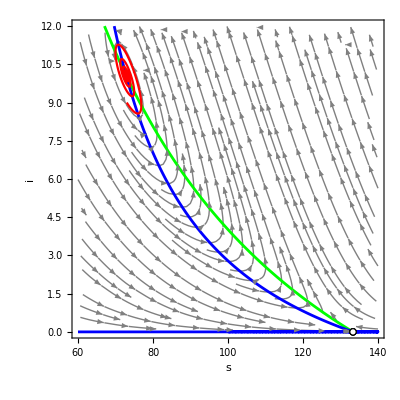

Final time slice is

1000.

The floquet exponents are

{-0.0165711+0.00275759 ⅈ,-0.0165711-0.00275759 ⅈ}

sp0B1.pdf

sol0B1.pdf

```mathematica
ClearParameters;
T=300;
xM=140;
xm=60;
yM=12;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;
w=901/195//N
α=60367/14625//N
Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]]+1,i->IntegerPart[eq[[2,2]][[2]]]-1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["sp0B1.pdf",sp]
Export["sol0B1.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (Between BT and B1):

6.25

5.58333

Fixed points:

{{s→133.333,i→0.},{s→93.5174,i→5.13535}}

Eigenvalues of FP:

{{-0.12,0},{0.0226741+0.0987278 ⅈ,0.0226741-0.0987278 ⅈ}}

Time plot around E2

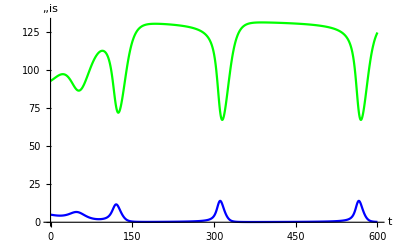

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

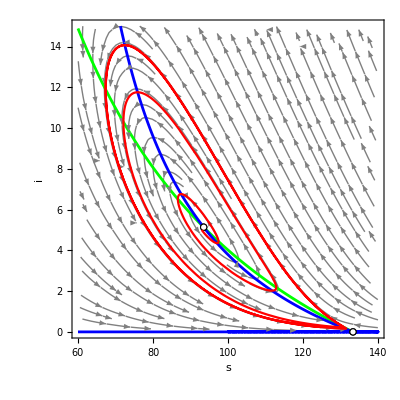

Final time slice is

254.473

The floquet exponents are

{-4.59451×10^-8,-0.0659782}

spB12E.pdf

solT12.pdf

```mathematica
ClearParameters;
T=600;
xM=140;
xm=60;
yM=15;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=25/4 //N
α=67/12//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB12E.pdf",sp]
Export["solT12.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (Between BT and B1):

5.27737

4.71445

Fixed points:

{{s→133.333,i→0.},{s→77.724,i→8.66002}}

Eigenvalues of FP:

{{-0.12,0.0203162},{-0.00353726+0.157026 ⅈ,-0.00353726-0.157026 ⅈ}}

Time plot around E2

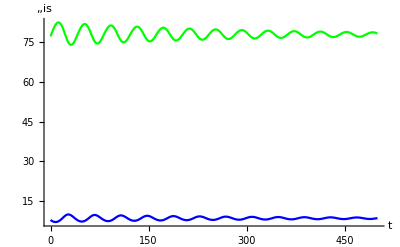

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

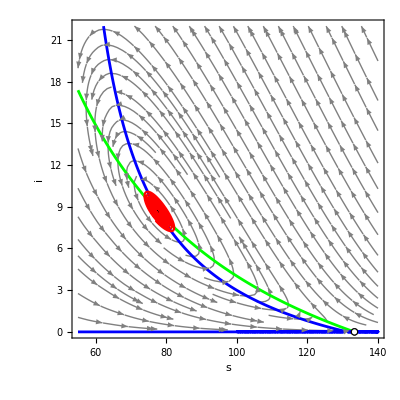

Final time slice is

40.1628

The floquet exponents are

{-0.00353727+0.000583175 ⅈ,-0.00353727-0.000583175 ⅈ}

spB12aE.pdf

solT12a.pdf

```mathematica
ClearParameters;
T=500;
xM=140;
xm=55;
yM=22;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=723/137//N 
α=16147/3425//N
ω=5.157354044656745;α=4.607236279893359;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB12aE.pdf",sp]
Export["solT12a.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (between B1 and BT):

5.61538

5.01641

Fixed points:

{{s→133.333,i→0.},{s→84.1709,i→7.05842}}

Eigenvalues of FP:

{{-0.12,0},{0.0122452+0.131269 ⅈ,0.0122452-0.131269 ⅈ}}

Time plot around E2

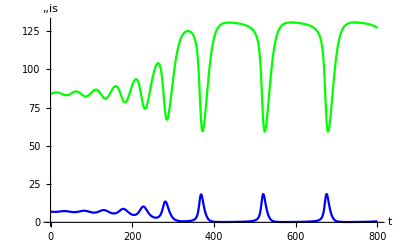

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

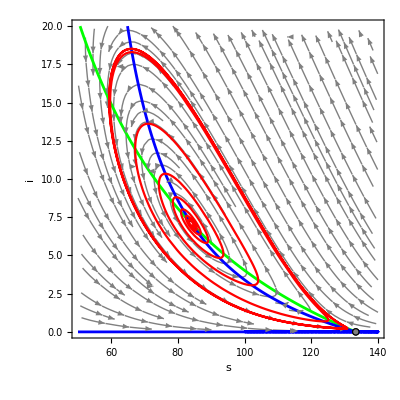

Final time slice is

155.023

The floquet exponents are

{2.50718×10^-8,-0.0534859}

spBP1E.pdf

solBP1.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=50;
yM=20;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=73/13//N
α=4891/975//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBP1E.pdf",sp]
Export["solBP1.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (another between B1 and BT):

6.09375

5.44375

Fixed points:

{{s→133.333,i→0.},{s→91.0252,i→5.60883}}

Eigenvalues of FP:

{{-0.12,0},{0.0210629+0.10705 ⅈ,0.0210629-0.10705 ⅈ}}

Time plot around E2

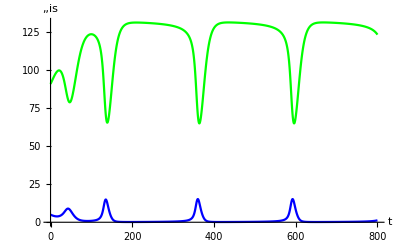

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

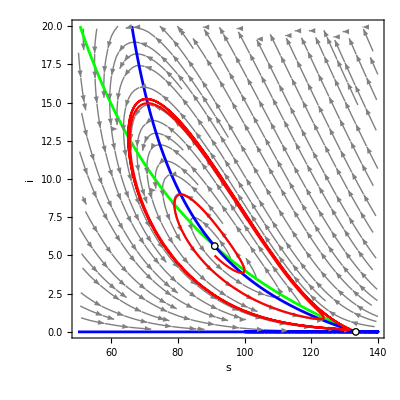

Final time slice is

231.915

The floquet exponents are

{8.82425×10^-10,-0.0647755}

spBP2E.pdf

solBP2.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=50;
yM=20;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=195/32(*11/2*)//N
α=871/160(*737/150*)//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBP2E.pdf",sp]
Export["solBP2.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI ( between BT and B1 and closer to BT):

Fixed points:

{{s→133.333,i→0.},{s→92.4572,i→5.33361},{s→133.333,i→0.}}

Eigenvalues of FP:

{{-0.12,0},{0.022091+0.10223 ⅈ,0.022091-0.10223 ⅈ},{-0.12,0}}

Time plot around E2

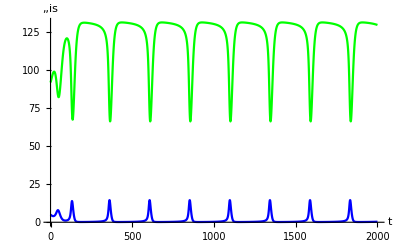

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

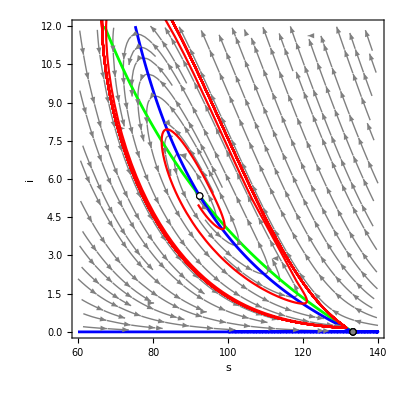

Final time slice is

245.34

The floquet exponents are

{3.41435×10^-8,-0.0656078}

```mathematica
ClearParameters;
T=2000;
xM=140;
xm=60;
yM=12;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;(*w=235/36;α=3149/540;*)
w=18362/2969;α=1230254/222675;
Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
(*Export["spHPE.pdf",sp]
Export["solHP.pdf",psol]*)
```

#### Phase plot of the boundary R0=1 between Regions IV and II (Between B2 and BT):

7.16058

6.39679

Fixed points:

{{s→133.333,i→0.},{s→111.34,i→2.376}}

Eigenvalues of FP:

{{-0.12,0},{0.0103906+0.0502167 ⅈ,0.0103906-0.0502167 ⅈ}}

Time plot around E2

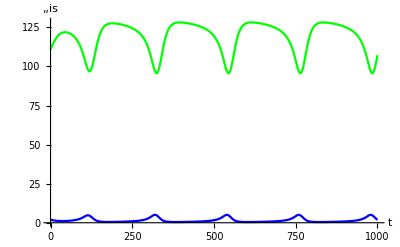

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

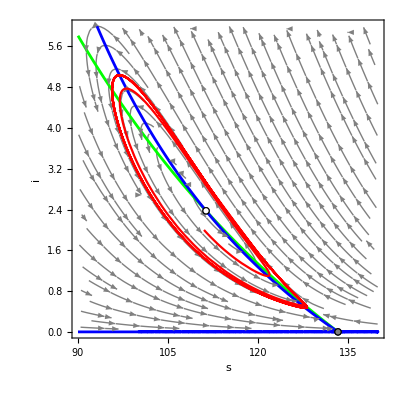

Final time slice is

219.938

The floquet exponents are

{-2.73386×10^-8,-0.0298991}

spB12bE.pdf

solT12b.pdf

```mathematica
ClearParameters;
T=1000;
xM=140;
xm=90;
yM=6;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=981/137//N
α=21909/3425//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB12bE.pdf",sp]
Export["solT12b.pdf",psol]
```

#### Phase plot of the boundary R0=1 (Between B2 and H:

Fixed points:

{{s→133.333,i→0.},{s→132.327,i→0.0913037}}

Eigenvalues of FP:

{{-0.12,3.36932×10^-8},{-0.11092,-0.0000418337}}

Time plot around E2

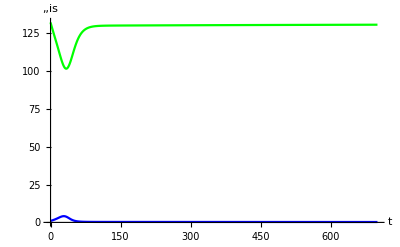

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

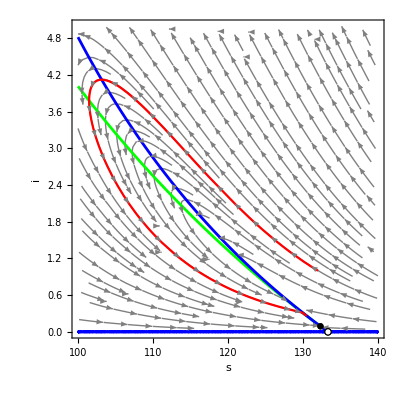

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spB2H.pdf

solB2H.pdf

```mathematica
ClearParameters;
T=700;
xM=140;
xm=100;
yM=5;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=Rationalize[7.91456];α=Rationalize[7.07034];

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]+1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB2H.pdf",sp]
Export["solB2H.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at BT):

Fixed points:

{{s→133.333,i→0.},{s→117.868,i→1.57702},{s→118.035,i→1.55773}}

Eigenvalues of FP:

{{-0.12,-0.0133232},{0.000211533+0.00400187 ⅈ,0.000211533-0.00400187 ⅈ},{-0.00420604,0.00378029}}

Time plot around E2

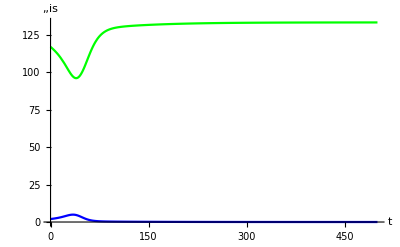

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

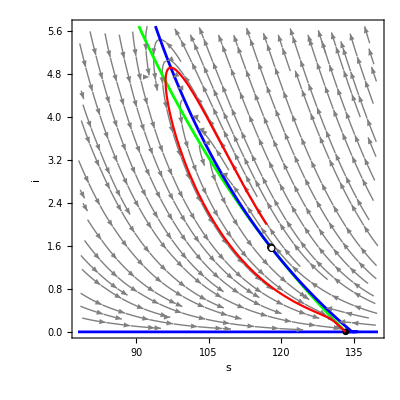

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spBTPE.pdf

solBTP.pdf

```mathematica
ClearParameters;
T=500;
xM=140;
xm=78;
yM=5.7;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=Rationalize[6.84183];
α=Rationalize[6.20319];

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]+1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBTPE.pdf",sp]
Export["solBTP.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at B2):

Fixed points:

{{s→133.333,i→0.},{s→116.198,i→1.77273},{s→133.333,i→6.08086×10^-6}}

Eigenvalues of FP:

{{-0.12,-5.43503×10^-8},{-3.10229×10^-7+0.0391095 ⅈ,-3.10229×10^-7-0.0391095 ⅈ},{-0.119999,5.43504×10^-8}}

Time plot around E2

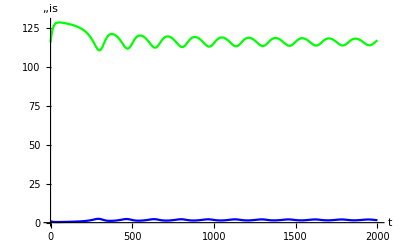

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

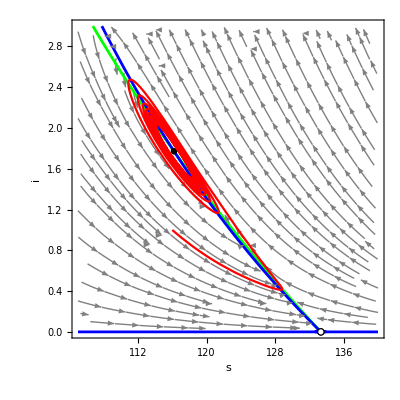

Final time slice is

160.802

The floquet exponents are

{-0.0000427718,-0.0000520552}

spB2E.pdf

solB2.pdf

```mathematica
ClearParameters;
T=2000;
xM=140;
xm=105;
yM=3;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=Rationalize[7.35966];α=Rationalize[6.57463];

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB2E.pdf",sp]
Export["solB2.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at B1):

Fixed points:

{{s→133.333,i→0.},{s→78.5252,i→8.44637},{s→133.333,i→0.000023398}}

Eigenvalues of FP:

{{-0.12,-1.42192×10^-6},{3.74007×10^-7+0.152171 ⅈ,3.74007×10^-7-0.152171 ⅈ},{-0.119998,1.42194×10^-6}}

Time plot around E2

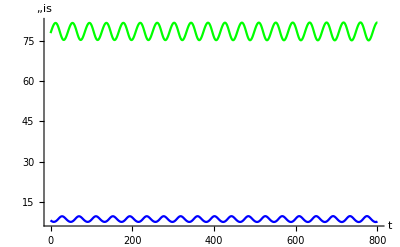

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

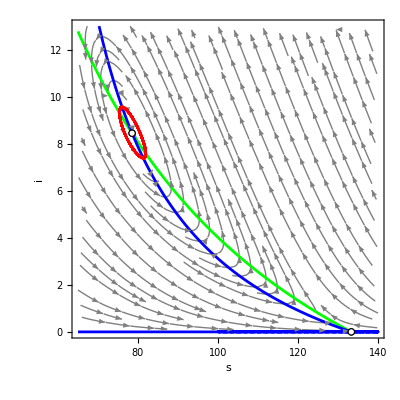

Final time slice is

42.2395

The floquet exponents are

{0.00184059,-0.000203924}

spBPE.pdf

solBP.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=65;
yM=13;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=5.15735;
α=4.60724;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBPE.pdf",sp]
Export["solBP.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at H):

7.09723

Fixed points:

{{s→133.333,i→0.},{s→133.239,i→0.00845707}}

Eigenvalues of FP:

{{-0.12,3.33333×10^-7},{-0.119146,-6.71449×10^-7}}

Time plot around E2

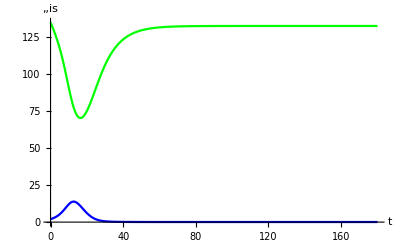

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

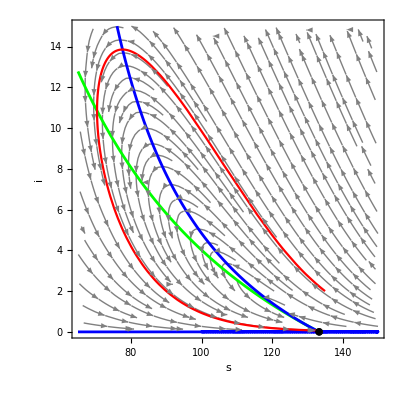

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spHPE.pdf

solHP.pdf

```mathematica
ClearParameters;
T=180;
xM=150;
xm=65;
yM=15;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=7.94466;
α=w *0.893333

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]]+2,i->IntegerPart[eq[[2,2]][[2]]]+2},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spHPE.pdf",sp]
Export["solHP.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions II and IV (After HP):

7.34375

6.56042

Fixed points:

{{s→133.333,i→0.},{s→115.794,i→1.82095}}

Eigenvalues of FP:

{{-0.12,0},{0.000976665+0.0400896 ⅈ,0.000976665-0.0400896 ⅈ}}

Time plot around E2

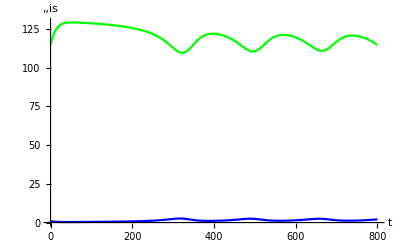

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

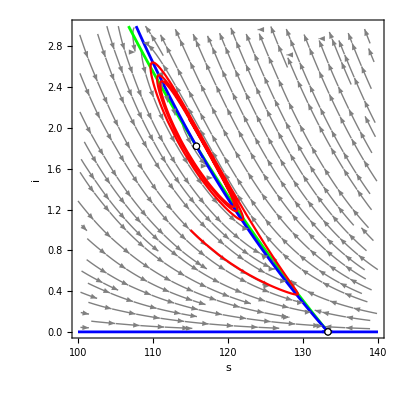

Final time slice is

163.987

The floquet exponents are

{-9.18309×10^-8,-0.00203132}

spB24E.pdf

solB24.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=100;
yM=3;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;xi=1/1000;μ=12/100;w=235/32//N
α=3149/480//N


Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB24E.pdf",sp]
Export["solB24.pdf",psol]
```

# Gupta figures:

#### Phase plot of Fig 1 a) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.35294,i→0.249912},{s→3.87623,i→0.146443}}

Eigenvalues of E2,E0,E1:

{{-0.3,-0.1},{0.012018+0.0764974 ⅈ,0.012018-0.0764974 ⅈ},{0.121831,-0.0411935}}

Time plot around DFE

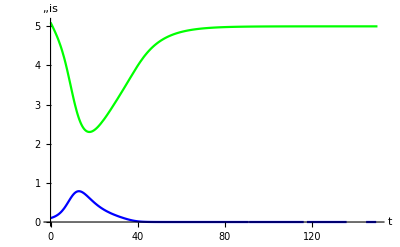

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

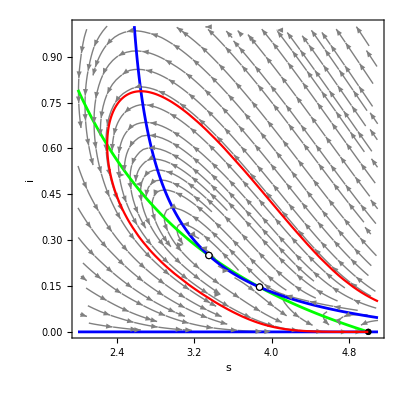

Final time slice is

453.519

The floquet exponents are

{-∞,-∞}

spGaE.pdf

solGa.pdf

```mathematica
ClearParameters;
T=150;
xM=5.1;
xm=2;
yM=1;
ym=0;
Λ=1/2 ;δ=1/5;γ=1/10;β=1/5;xi=7/100;μ=1/10;

w= 10/99;α=1/11;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of E2,E0,E1:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-9]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around DFE"]
sol=EcoSim[{s->5.1,i->0.1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGaE.pdf",sp]
Export["solGa.pdf",psol]
```

#### Phase plot of Fig 1 b) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.1916,i→0.289038},{s→4.03079,i→0.121247}}

Eigenvalues of E2,E0,E1:

{{-0.3,-0.1},{5.58554×10^-6+0.101011 ⅈ,5.58554×10^-6-0.101011 ⅈ},{0.144435,-0.0530554}}

Time plot around E2

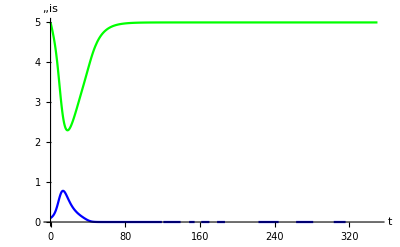

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

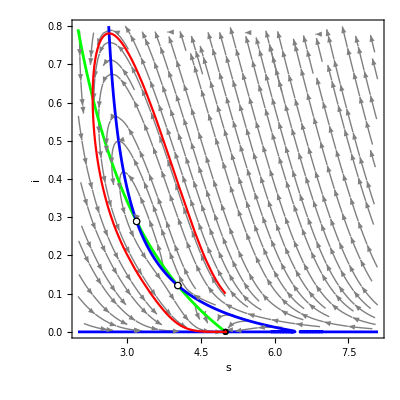

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spGbE.pdf

solGb.pdf

```mathematica
T=350;
xM=8.1;
xm=2;
yM=.8;
Λ=1/2 ;δ=1/5;γ=1/10;β=1/5;xi=7/100;μ=1/10;
w=10000/103387;α=9000/103387;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of E2,E0,E1:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->5,i->0.1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGbE.pdf",sp]
Export["solGb.pdf",psol]
```

#### Phase plot of Fig 1 c) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.08116,i→0.318321},{s→4.13484,i→0.105391}}

Eigenvalues of FP:

{{-0.3,-0.1},{-0.00915663+0.115223 ⅈ,-0.00915663-0.115223 ⅈ},{0.156612,-0.0594875}}

Time plot around DFE

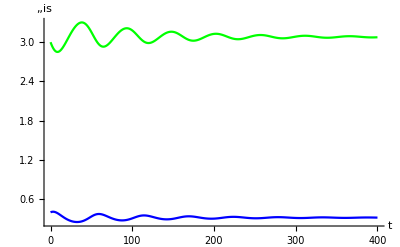

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

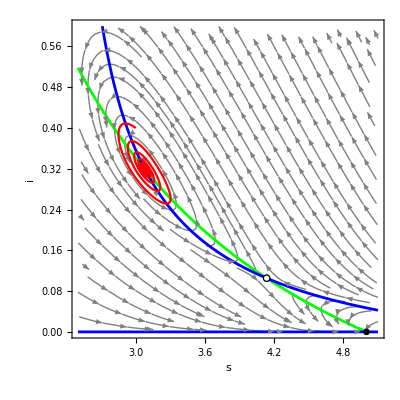

Final time slice is

1000.

The floquet exponents are

{-0.00915701+0.00212584 ⅈ,-0.00915701-0.00212584 ⅈ}

spGcE.pdf

solGc.pdf

Time plot around DFE

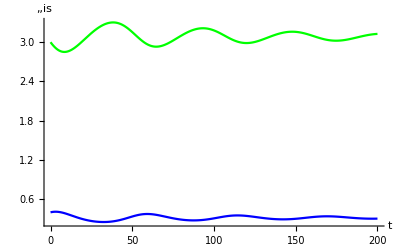

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

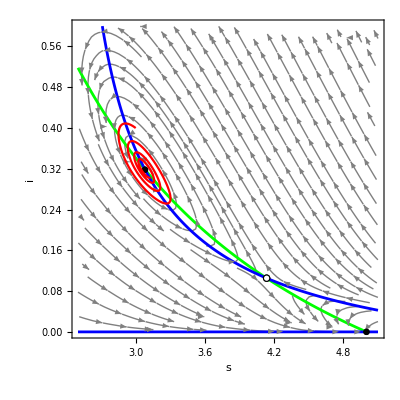

Final time slice is

19.1064

The floquet exponents are

{-0.00915663+0.115223 ⅈ,-0.00915663-0.115223 ⅈ}

spGcE.pdf

solGc.pdf

```mathematica
T=400;
xm=2.5;
yM=0.6;
Λ=1/2 ;δ=1/5;γ=1/10;β=1/5;xi=7/100;μ=1/10;
w=5/54;α=1/12;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-5]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around DFE"]
sol=EcoSim[{s->3,i->0.4},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGcE.pdf",sp]
Export["solGc.pdf",psol]
```

#### Phase plot of Fig 1 d) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.04252,i→0.329097},{s→4.17091,i→0.100086}}

Eigenvalues of FP:

{{-0.3,-0.1},{-0.0125465+0.119857 ⅈ,-0.0125465-0.119857 ⅈ},{0.160369,-0.0615297}}

Time plot around E2

-Graphics-

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

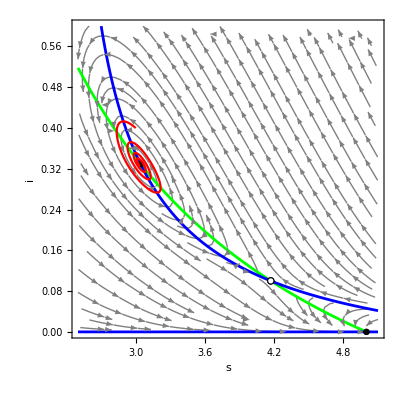

Final time slice is

19.1064

The floquet exponents are

{-0.00851491+0.114365 ⅈ,-0.00851491-0.114365 ⅈ}

spGdE.pdf

solGd.pdf

```mathematica
T=180;
xm=2.5;
yM=0.6;
w=1/11;α=9/110;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-5]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->3,i->0.4},T];
psol
Print["Finding the cycle using time slice"]
lc
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGdE.pdf",sp]
Export["solGd.pdf",psol]
```

#### Phase plot of Fig 3a) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.11718,i→0.308529},{s→4.10105,i→0.110447}}

Eigenvalues of E2,E0,E1:

{{-0.3,-0.1},{-0.00608274+0.110756 ⅈ,-0.00608274-0.110756 ⅈ},{0.152885,-0.0574955}}

Time plot around E2

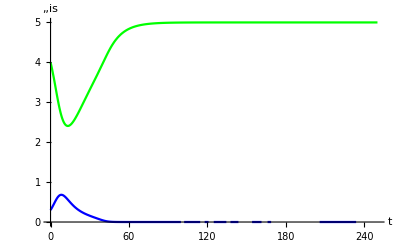

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

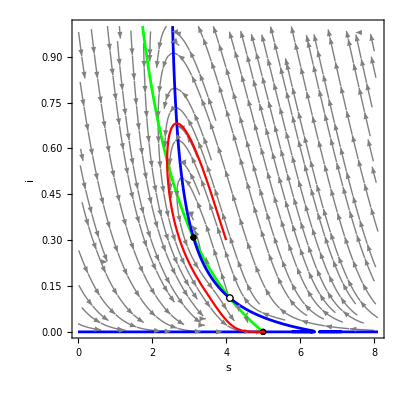

Final time slice is

648.762

The floquet exponents are

{-∞,-∞}

spG3aE.pdf

solG3a.pdf

```mathematica
T=250;
xM=8.1;
xm=0;
yM=1;

w=100000000/1063265757;α=30000000/354421919;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of E2,E0,E1:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->4,i->0.3},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spG3aE.pdf",sp]
Export["solG3a.pdf",psol]
```

```mathematica
25/4//N
67/12//N
```

6.25

5.58333